```mathematica
Clear["Global`*"];
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
um=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
mCs=132.90545 amu;mNa = 23amu;
a0= 5.2917721067 10^-11;
ϵ0=8.854187817 10^-12;
c=299792458;
cm=10^-2;
ms=10^-3;
ωrCs=2π 150kHz;
ωaCs=2π 25kHz;
ωrNa=2π 150kHz;
ωaNa=2π 25kHz;
μ=(mNa mCs)/(mCs+mNa);
```

```mathematica
Clear[δ,ρ0]
(*basis: 
1 |n1,Down>
2 |n1,Up>
3 |n2,Down>
4 |n2,Up>
*)
ωtr=ωrCs;
cn1=1; (*start all in spin down*)

ρ0=SparseArray[{{2,2}}->{Abs[cn1]^2}];
Hdet=1/2 δ DiagonalMatrix[{1,-1}];
HR=Ω0/2 SparseArray[{{1,2},{2,1}}->{1,1}];
Hint=DiagonalMatrix[{0,Δ}];

Htot=HR+Hint+Hdet;

Htot//MatrixForm
```

(δ/2 | Ω0/2
Ω0/2 | -δ/2+Δ)

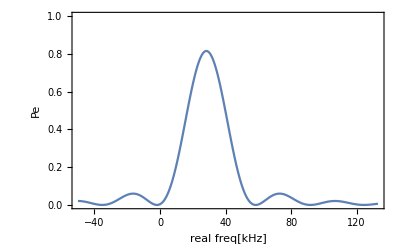

Ω0/2πkHz | Δ/2πkHz | t/us
11.57 | 28.3 | 30

```mathematica
f[ρ0_,δ0_]:=Block[{δ=δ0,ρ=ρ0},-I (Htot.ρ-ρ.Htot)];
Ω0=2π 11.57kHz;
Δ=2π 28.3kHz;

Δt=1us;
tEnd=30us;
(*take spectrum*)
sim=Reap[
Do[
ρ1=ρ0;
Do[
k1=Δt f[ρ1,δ];
k2=Δt f[ρ1+k1/2,δ];
k3=Δt f[ρ1+k2/2,δ];
k4=Δt f[ρ1+k3,δ];
ρ1=ρ1+1/3(k1/2+k2+k3+k4/2),
{i,0,Ceiling[tEnd/Δt]}
]
Sow[{δ/(2π kHz),ρ1[[1,1]]}]
,{δ,-2π 50kHz,2π 133kHz,2π .3kHz}
]
][[2,1]];

ListPlot[Chop[sim],Joined->True,PlotRange->{All,{0,1}},Axes->False,Frame->True,FrameLabel->{"real freq[kHz]","Pe"},LabelStyle->{Black,17}]
{{"Ω0/2πkHz","Δ/2πkHz","t/us"},{Ω0/(2π kHz),Δ/(2π kHz),tEnd/us}}//TableForm
```